```mathematica
Needs["Strategies`",NotebookDirectory[]<>"Strategies.m"] (* Load Pegasus strategies package from current directory *)
```

```mathematica
(*** Pegasus examples ***)

(* EXAMPLE 1 *)
(* Specify safety verification problem as a triple { INIT, {ODE_SYSTEM, STATE_VARS, EVOLUTION_CONSTRAINT}, SAFE }  *)
safetyProblem1 = {(Subscript[x, 1]-2)^2+Subscript[x, 2]^2≤1/5 || (Subscript[x, 1]+2)^2+(Subscript[x, 2]-2)^2≤1/3, {{-4 Subscript[x, 2], Subscript[x, 1]},{Subscript[x, 1],Subscript[x, 2]}, True},  Subscript[x, 2]≤4 && Subscript[x, 2]≥-4 &&Not[Subscript[x, 1]^2+Subscript[x, 2]^2≤1/3]};

(* Call Pegasus to generate invariant (displayed as output on final line) *)
invariant1 = Pegasus[safetyProblem1]
```

Precondition is not equal to the postcondition. Proceeding.

Non-zero vector field. Proceeding.

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Pretcondition is not an invariant. Proceeding.

PLANAR LINEAR STRATEGY

{82/7-x_1^2-4 x_2^2,185/6-x_1^2-4 x_2^2}

DC on 82/7-x_1^2-4 x_2^2≤0

DC on 185/6-x_1^2-4 x_2^2≥0

DW

{53/22-x_1^2-4 x_2^2,6-x_1^2-4 x_2^2}

DC on 53/22-x_1^2-4 x_2^2≤0

DC on 6-x_1^2-4 x_2^2≥0

DW

Generated invariant implies postcondition. Returning.

{(82/7-x_1^2-4 x_2^2≤0&&185/6-x_1^2-4 x_2^2≥0)||(53/22-x_1^2-4 x_2^2≤0&&6-x_1^2-4 x_2^2≥0),True}

```mathematica
(* Visualize safety verification problem and generated invariant *)
```

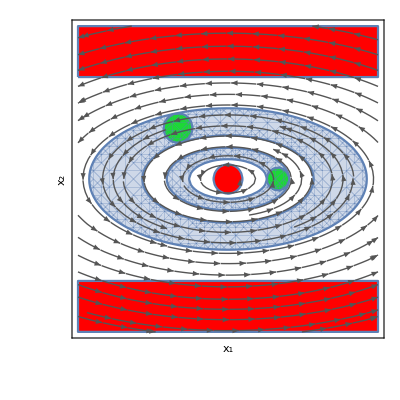

```mathematica
{ init1,{ f1,vars1,H1 }, safe1 }=safetyProblem1;
{x1min,x1max}={-6,6};
{x2min, x2max}={-6,6};

Show[
RegionPlot[Not[safe1],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init1,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant1[[1]],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f1,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

Precondition is not equal to the postcondition. Proceeding.

Non-zero vector field. Proceeding.

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Pretcondition is not an invariant. Proceeding.

PLANAR CONSTANT STRATEGY

{-73/10-2 x_1+x_2,-47/10-2 x_1+x_2,-56/17+x_1+2 x_2,-17/24+x_1+2 x_2}

DC on -73/10-2 x_1+x_2≤0

DC on -47/10-2 x_1+x_2≥0

DW

{37/21-2 x_1+x_2,181/29-2 x_1+x_2,-106/25+x_1+2 x_2,13/55+x_1+2 x_2}

DC on 37/21-2 x_1+x_2≤0

DC on 181/29-2 x_1+x_2≥0

DC on 13/55+x_1+2 x_2≥0

No more cuts ...

Generated invariant does not imply postcondition. Bad luck; returning what I could find.

{(-73/10-2 x_1+x_2≤0&&-47/10-2 x_1+x_2≥0)||(37/21-2 x_1+x_2≤0&&181/29-2 x_1+x_2≥0&&13/55+x_1+2 x_2≥0),False}

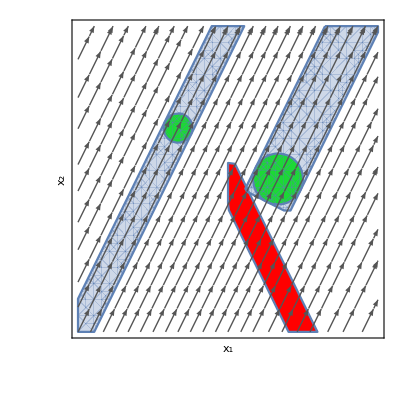

```mathematica
safetyProblem1c = {(Subscript[x, 1]-2)^2+Subscript[x, 2]^2≤1 || (Subscript[x, 1]+2)^2+(Subscript[x, 2]-2)^2≤1/3, {{1, 2},{Subscript[x, 1],Subscript[x, 2]}, True},  (-1/2 Subscript[x, 2]-Subscript[x, 1])^2≥1/3 || Subscript[x, 1]<=0};
invariant1c = Pegasus[safetyProblem1c]

{ init1c,{ f1c,vars1c,H1c }, safe1c }=safetyProblem1c;
{x1min,x1max}={-6,6};
{x2min, x2max}={-6,6};

Show[
RegionPlot[Not[safe1c],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init1c,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant1c[[1]],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f1c,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

```mathematica
(* EXAMPLE 2 *)
(* Specify safety verification problem as a triple { INIT, ODE_SYSTEM, SAFE }  *)
safetyProblem2 = {(Subscript[x, 1]-2)^2+Subscript[x, 2]^2≤1/5 || (Subscript[x, 1]+2)^2+(Subscript[x, 2]-2)^2≤1/3, {{2 Subscript[x, 1]-Subscript[x, 2], -3*Subscript[x, 1]+Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}, True},  (Subscript[x, 1]-1)^2+(Subscript[x, 2]+5)^2≥2};

(* Call Pegasus to generate invariant (displayed as output on final line) *)
invariant2 = Pegasus[safetyProblem2]
```

Precondition is not equal to the postcondition. Proceeding.

Non-zero vector field. Proceeding.

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Pretcondition is not an invariant. Proceeding.

PLANAR LINEAR STRATEGY

{}

{-(23 x_1)/10+x_2,(30 x_1)/23+x_2}

{-(23 x_1)/10+x_2,(30 x_1)/23+x_2}

{-137/17-(23 x_1)/10+x_2,-36/7-(23 x_1)/10+x_2,-(23 x_1)/10+x_2,-15/44+(30 x_1)/23+x_2,(30 x_1)/23+x_2,39/25+(30 x_1)/23+x_2}

No more cuts ...

{}

{-(23 x_1)/10+x_2,(30 x_1)/23+x_2}

{-(23 x_1)/10+x_2,(30 x_1)/23+x_2}

{-(23 x_1)/10+x_2,66/19-(23 x_1)/10+x_2,63/11-(23 x_1)/10+x_2,-77/23+(30 x_1)/23+x_2,-73/39+(30 x_1)/23+x_2,(30 x_1)/23+x_2}

No more cuts ...

Generated invariant does not imply postcondition. Bad luck; returning postcondition.

True

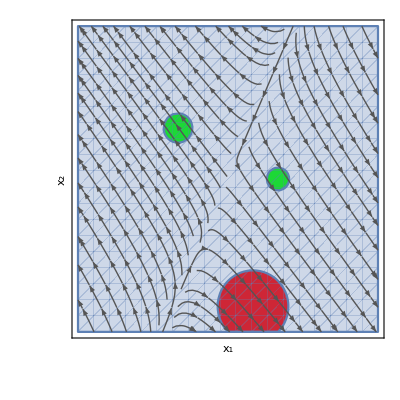

```mathematica
(* Visualize safety verification problem and generated invariant *)
{ init2,{ f2,vars2,H2 }, safe2 }=safetyProblem2;
{x1min,x1max}={-6,6};
{x2min, x2max}={-6,6};

Show[
RegionPlot[Not[safe2],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init2,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant2,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f2,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

```mathematica
(* EXAMPLE 3 *)
(* Specify safety verification problem as a triple { INIT, ODE_SYSTEM, SAFE }  *)
safetyProblem3 = {(Subscript[x, 1]-2)^2+Subscript[x, 2]^2≤1/5 || (Subscript[x, 1]+2)^2+(Subscript[x, 2]-2)^2≤1/3, {{-2 Subscript[x, 1]+Subscript[x, 2], Subscript[x, 1]-3*Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}, True},  Not[(Subscript[x, 2]≥1)&&(Subscript[x, 1]≤1 && Subscript[x, 1]≥0) || (Subscript[x, 1])^2+(Subscript[x, 2]+3)^2≤1]};

(* Call Pegasus to generate invariant (displayed as output on final line) *)
invariant3 = Pegasus[safetyProblem3]
```

DC on (2 x_1)/(-1+√5)+x_2≤0

DC on -1+√5-(2 √(1/3 (5-2 √5)))/(-3+√5)+(2 x_1)/(-1+√5)+x_2≥0

DC on -(2 x_1)/(1+√5)+x_2≥0

DC on (2 x_1)/(-1+√5)+x_2≥0

DC on -1-√5+(2 √(1-2/(√5)))/(-3+√5)+(2 x_1)/(-1+√5)+x_2≤0

DC on -(2 x_1)/(1+√5)+x_2≤0

(2 x_1+√5 x_2≤x_2&&√5+(2 x_1)/(-1+√5)+x_2≥1+(2 √(1/3 (5-2 √5)))/(-3+√5)&&(1+√5) x_2≥2 x_1)||(2 x_1+√5 x_2≥x_2&&(2 √(1-2/(√5)))/(-3+√5)+(2 x_1)/(-1+√5)+x_2≤1+√5&&(1+√5) x_2≤2 x_1)

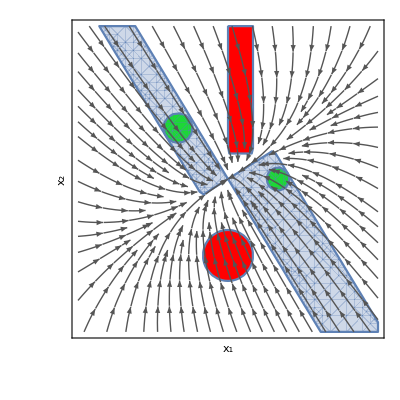

```mathematica
(* Visualize safety verification problem and generated invariant *)
{ init3,{ f3,vars3,H3 }, safe3 }=safetyProblem3;
{x1min,x1max}={-6,6};
{x2min, x2max}={-6,6};

Show[
RegionPlot[Not[safe3],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init3,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant3,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f3,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

```mathematica
(* EXAMPLE 4 - One dimensonal problem *)
(* Specify safety verification problem as a triple { INIT, ODE_SYSTEM, SAFE }  *)
safetyProblem4 = {x≤0,{{-5*x^2+x^3+2x +3},{x},True}, x≤10};

(* Call Pegasus to generate invariant *)
invariant4 = Pegasus[safetyProblem4]
```

x<Root[3+2 #1-5 #1^2+#1^3&,2]

```mathematica
(* Numericize invariant to get rid of real algebraic numbers *)
N[invariant4]
```

x<1.18728

```mathematica
(* EXAMPLE 5 - Nonlinear system. ODE from Dumortier, Llibre & Artes, Exercise 10.6. *)
(* Specify safety verification problem as a triple { INIT, ODE_SYSTEM, SAFE }  *)
safetyProblem5 = {(Subscript[x, 1]-1)^2+(Subscript[x, 2])^2<1/4, {{(-1+Subscript[x, 1]^2) (-(-2+√5)^2+Subscript[x, 1]^2) (Subscript[x, 1]+√5 Subscript[x, 2]),(√5 Subscript[x, 1]+Subscript[x, 2]) (-1+Subscript[x, 2]^2) (-(-2+√5)^2+Subscript[x, 2]^2)},{Subscript[x, 1],Subscript[x, 2]}, True},  Subscript[x, 2]<1};

(* Call Pegasus to generate invariant (displayed as output on final line) *)
invariant5 = Pegasus[safetyProblem5]
```

DC on -1+x_2≤0

No more cuts ...

DC on 1+x_1≥0

DC on 2-√5+x_1≥0

DC on -2+√5+x_1≥0

DC on -1+x_2≤0

DC on 1+x_2≥0

DC on √5 x_1+x_2≥0

No more cuts ...

DC on 1+x_1≥0

DC on 2-√5+x_1≥0

DC on -2+√5+x_1≥0

DC on -1+x_2≤0

DC on 1+x_2≥0

DC on √5 x_1+x_2≥0

No more cuts ...

DC on -2+√5-x_1≤0

DC on -2+√5+x_1≥0

DC on 1+x_1≥0

DC on -1+x_2≤0

DC on 1+x_2≥0

DC on √5 x_1+x_2≥0

No more cuts ...

DC on -1+x_2<0

-1≤x_2≤1&&2+x_1≥√5&&√5 x_1+x_2≥0&&-1+x_2<0

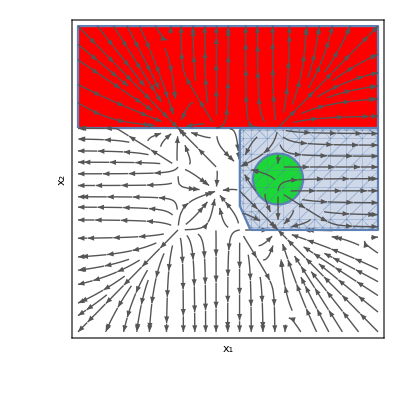

```mathematica
{ init5,{ f5,vars5,H5 }, safe5 }=safetyProblem5;
{x1min,x1max}={-3,3};
{x2min, x2max}={-3,3};

Show[
RegionPlot[Not[safe5],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init5,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant5,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f5,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

No more cuts ...

DC on x_1≤0

DC on x_1+x_1^2 x_2+x_2^3≥0

x_1≤0&&x_1+x_1^2 x_2+x_2^3≥0

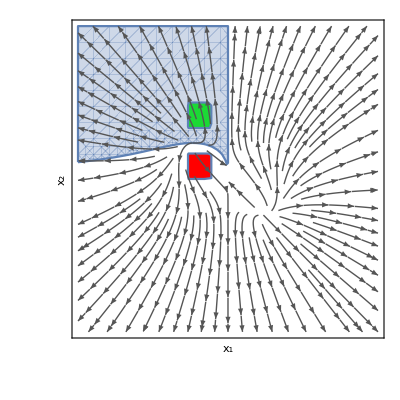

```mathematica
(* Nonlinear ODE from Strogatz, Example 6.3.2 *)
safetyProblem6 = {Subscript[x, 1]>-4/5&&Subscript[x, 1]<-1/3&&Subscript[x, 2]<3/2&&Subscript[x, 2]≥1, {{-Subscript[x, 1]+a*Subscript[x, 1](Subscript[x, 1]^2+Subscript[x, 2]^2), Subscript[x, 1]+a*Subscript[x, 2](Subscript[x, 1]^2+Subscript[x, 2]^2)}/.{a->1},{Subscript[x, 1],Subscript[x, 2]}, True},  Subscript[x, 1]≥-1/3||Subscript[x, 2]<0||2 Subscript[x, 2]≥1||Subscript[x, 1]≤-4/5};
invariant6=Pegasus[safetyProblem6]

{ init6,{ f6,vars6,H6 }, safe6 }=safetyProblem6;
{x1min,x1max}={-3,3};
{x2min, x2max}={-3,3};

Show[
RegionPlot[Not[safe6],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init6,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant6,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f6,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

No more cuts ...

DC on -1+x_1≤0

DC on 1+x_1≥0

-1≤x_1≤1

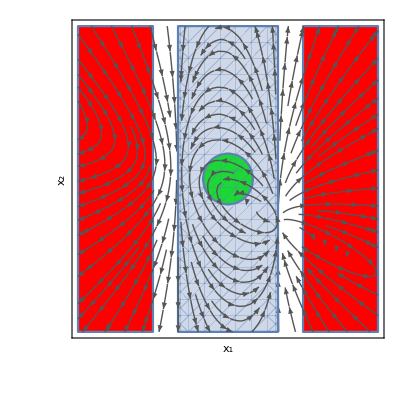

```mathematica
(* Nonlinear ODE from Dumortier, Llibre & Artes, Exercise 10.11 *)
safetyProblem7 = {Subscript[x, 1]^2+Subscript[x, 2]^2<1/4, {{-70-100 Subscript[x, 1]+70 Subscript[x, 1]^2+100 Subscript[x, 1]^3-200 Subscript[x, 2]+200 Subscript[x, 1]^2 Subscript[x, 2],146 Subscript[x, 1]+100 Subscript[x, 2]+140 Subscript[x, 1] Subscript[x, 2]+100 Subscript[x, 1]^2 Subscript[x, 2]+200 Subscript[x, 1] Subscript[x, 2]^2},{Subscript[x, 1],Subscript[x, 2]}, True},  Subscript[x, 1]>-3/2 && Subscript[x, 1]<3/2};
invariant7=Pegasus[safetyProblem7]

{ init7,{ f7,vars7,H7 }, safe7 }=safetyProblem7;
{x1min,x1max}={-3,3};
{x2min, x2max}={-3,3};

Show[
RegionPlot[Not[safe7],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init7,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant7,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f7,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

No more cuts ...

No more cuts ...

No more cuts ...

«1 more identical outputs»

No more cuts. Trying LazyReach with |A|=3

LazyReach with 3 abstraction polynomials (at most 27 discrete states and 316 neighbouring transitions).

Total number of discrete states: 15

Number of neighbouring transitions: 90

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3<0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3<0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3<0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3<0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3<0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2>0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

Validating transition {True,-2+x_2>0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}

Validating transition {True,-2+x_2==0,x_1+2 x_1^2-x_2+3 x_1 x_2^2<0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3>0}->{True,-2+x_2<0,x_1+2 x_1^2-x_2+3 x_1 x_2^2==0,2 x_1+3 x_1^2+4 x_1 x_2+6 x_2^3==0}

(x_2<2||3 x_1^2+6 x_2^3+x_1 (2+4 x_2)>0)&&(x_1 (1+2 x_1+3 x_2^2)≠x_2||3 x_1^2+6 x_2^3+x_1 (2+4 x_2)≠0)

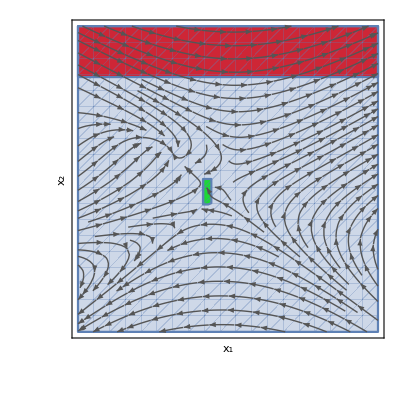

```mathematica
(* Pegasus is NOT guaranteed to succeed, as in this example where even the expensive fallback option of computing a qualitative abstraction fails to find an invariant that is sufficient to prove the safety property. Nonlinear ODE from Dumortier, Llibre & Artes, Exercise 2.11. *)
safetyProblem8 = {(Subscript[x, 1]>-1/2 && Subscript[x, 1]<-1/3 && Subscript[x, 2]<0 && Subscript[x, 2]≥- 1/2), {{2*Subscript[x, 1]+3*Subscript[x, 1]^2+4*Subscript[x, 1]*Subscript[x, 2]+6*Subscript[x, 2]^3, -Subscript[x, 2]+Subscript[x, 1]+2*Subscript[x, 1]^2+3*Subscript[x, 1]*Subscript[x, 2]^2},{Subscript[x, 1],Subscript[x, 2]}, True}, ( Subscript[x, 2] ≤2)};
invariant8=Pegasus[safetyProblem8]

{ init8,{ f8,vars8,H8 }, safe8 }=safetyProblem8;
{x1min,x1max}={-3,3};
{x2min, x2max}={-3,3};

Show[
RegionPlot[Not[safe8],{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Red,FrameLabel->{"x_1","x_2"}, FrameTicks->None,LabelStyle->Directive[Large]], (* Plot unsafe states in red *)
RegionPlot[init8,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, PlotStyle->Green], (* Plot initial states in green *)
RegionPlot[invariant8,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}], (* Plot invariant *)
StreamPlot[f8,{Subscript[x, 1],x1min,x1max},{Subscript[x, 2],x2min,x2max}, StreamStyle->Darker[Gray]] (* Plot vector field *)
]
```

```mathematica
(* EXAMPLE Robix *)
(* Specify safety verification problem as a triple { INIT, ODE_SYSTEM, SAFE }  *)
safetyProblemRobix = {x==1&&y==0&&dx==1 && dy==0, {{v*dx, v*dy, -w*dy, w*dx}/.{w->1,v->1},{x,y,dx,dy}, True},  Not[(x==0&&y==1&&dy==1 &&dx==0) ||(x==0 &&y==0)]};
ClassifyProblem[safetyProblemRobix]
(* Call Pegasus to generate invariant (displayed as output on final line) *)
invariantRobix = Pegasus[safetyProblemRobix]
```

{4,{Linear}}

GENERAL LINEAR STRATEGY

CENTRE!

{dx+y,-dy+x,dx^2+dy^2}

{-1+dx^2+dy^2,-1-dy+x,-1+dx+y}

DC on -1+dx^2+dy^2≥0

DC on -1-dy+x≥0

DC on -1+dx+y≥0

No more cuts ...

dx^2+dy^2≥1&&x≥1+dy&&dx+y≥1

```mathematica
(* EXAMPLE Robix *)
(* Specify safety verification problem as a triple { INIT, ODE_SYSTEM, SAFE }  *)
safetyProblemRobix2 = {x==1&&y==0&&dx==1 && dy==0, {{v*dx, v*dy, -w*dy, w*dx,0,0},{x,y,dx,dy,w,v}, True},  Not[(x==0&&y==0&&dy==1 &&dx==1) ||(x==0 &&y==0)]};
ClassifyProblem[safetyProblemRobix2]
(* Call Pegasus to generate invariant (displayed as output on final line) *)
invariantRobix2 = Pegasus[safetyProblemRobix2]
```

{6,{Multi-affine}}

MULTI-LINEAR STRATEGY

Running Strat

FuncIndep[{-w,-dx v-w y,dy v-w x,-w^2,-v,-v w,-v^2,-dx^2-dy^2}]

Union::heads: Heads FuncIndep and List at positions 2 and 1 are expected to be the same.

MaxValue::objfs: The objective function {} should be scalar-valued.

MinValue::objfs: The objective function {} should be scalar-valued.

Union::normal: Nonatomic expression expected at position 3 in {{},FuncIndep[{-w,-dx v-w y,dy v-w x,-w^2,-v,-v w,-v^2,-Power[«2»]-Power[«2»]}]-MinValue[{FuncIndep[{«8»}],Equal[«2»]&&Equal[«2»]&&Equal[«2»]&&Equal[«2»]},{x,y,dx,dy,w,v}]}∪{{},FuncIndep[{-w,-dx v-w y,dy v-w x,-w^2,-v,-v w,-v^2,-Power[«2»]-Power[«2»]}]-MaxValue[{FuncIndep[{«8»}],Equal[«2»]&&Equal[«2»]&&Equal[«2»]&&Equal[«2»]},{x,y,dx,dy,w,v}]}∪MultiLinear`Private`separatrices.

DWC[x==1&&y==0&&dx==1&&dy==0,!((x==0&&y==0&&dy==1&&dx==1)||(x==0&&y==0)),{{dx v,dy v,-dy w,dx w,0,0},{x,y,dx,dy,w,v},True},{{},FuncIndep[{-w,-dx v-w y,dy v-w x,-w^2,-v,-v w,-v^2,-dx^2-dy^2}]-MinValue[{FuncIndep[{-w,-dx v-w y,dy v-w x,-w^2,-v,-v w,-v^2,-dx^2-dy^2}],x==1&&y==0&&dx==1&&dy==0},{x,y,dx,dy,w,v}]}∪{{},FuncIndep[{-w,-dx v-w y,dy v-w x,-w^2,-v,-v w,-v^2,-dx^2-dy^2}]-MaxValue[{FuncIndep[{-w,-dx v-w y,dy v-w x,-w^2,-v,-v w,-v^2,-dx^2-dy^2}],x==1&&y==0&&dx==1&&dy==0},{x,y,dx,dy,w,v}]}∪MultiLinear`Private`separatrices]